The purpose of this notebook is to demonstrate the agreement between measured optical constants for Iron and the theoretical prediction modelling the conduction electrons as a plasma in a homogeneous background scattering incoherently off the ions.

```mathematica
Needs["Constants`"]
Needs["Utilities`"]
Needs["Dielectrics`"]
```

### Theoretical collision rate calculation a la Ziman

#### Incoherent Electron-Ion scattering collision rate

Ziman (1966) collision rate formula taken from eqn (3.80) pg 210 of Faber “Introduction to the Theory of Liquid Metals”

```mathematica
νZimanFaberLin[params_] :=( (4 "m" ("e")^4 ("Z")^2)/(π ("ℏ")^3 ("ϵ0")^2)/.params)("nI""qF"/.params)NIntegrate[z^3 (1/((2"qF")^2  z^2 ϵRPA0[z])/.params)^2  ,{z,0,1} ]
```

```mathematica
νZimanFaberLin[SIcrustparams]^-1
```

1.43325×10^-17

```mathematica
νZimanFaberLin[SIcrustparams]
```

6.97716×10^16

Note that this assumes the interference function (a(q)) is exactly 1. This is tantamount to assuming incoherent scattering off the ions

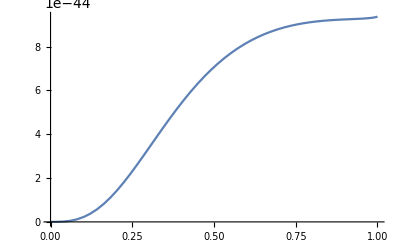

```mathematica
Plot[z^3 (1/((2"qF")^2  z^2 ϵRPA0[z])/.SIcrustparams)^2 ,{z,0,1}]
```

#### Collision rate from measured Resistivity

Collision rate for Iron from pg 10 of Ashcroft and Mermin at 273 K

```mathematica
τFeMermin = 0.24 10^-14
```

2.4×10^-15

```mathematica
τFeMermin^-1
```

4.16667×10^14

Comparing this value to the theoretical value above shows we are off by two orders of magnitude of the measured result!

The purpose of this notebook is to demonstrate the conflict between measured optical constants for Iron and the theoretical prediction modelling the conduction electrons as a plasma in a homogeneous background.

#### Compare to fitted collision rates

```mathematica
νZimanFaberLin[SIcrustparams]
```

6.97716×10^16

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparams"];
```

```mathematica
"νi"/.FeTotalparams
```

{1.75116×10^16,8.99966×10^15,2.01886×10^16,9.30837×10^16,7.408×10^17,5.21962×10^18}

```mathematica
"ωp"/.FeTotalparams
```

{5.0267×10^15,3.7972×10^15,6.21532×10^15,1.56117×10^16,5.65182×10^16,1.74803×10^17}

Note that the second oscillator corresponds to the value at the low energy tail of the distribution

### Extract Iron Data

This data is taken from a book of optical measurments by Palik (https://doi.org/10.1016/B978-012544415-6.50000-5 )

Data was extracted from Screenshots of tables in the book using  https://www.docsumo.com/free-tools/extract-tables-from-pdf-images

#### Import Data

```mathematica
opticaliron1 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_1.csv"][[2;;,;;3]];
opticaliron2 = Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_2.csv"][[2;;,;;3]];
opticaliron3 = ToExpression[Import["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\iron_optical_data\\optical_iron_3.csv"][[2;;,;;3]]];
```

#### Assign to variables

```mathematica
kFe= Join[opticaliron1[[;;,3]],opticaliron2[[;;,3]],opticaliron3[[;;,3]]]; (*[]*)
nFe= Join[opticaliron1[[;;,2]],opticaliron2[[;;,2]],opticaliron3[[;;,2]]]; (*[]*)
ωFe= Join[opticaliron1[[;;,1]],opticaliron2[[;;,1]],opticaliron3[[;;,1]]]; (*[eV]*)
```

#### Convert to ϵ

The following relation between k, n and ϵ where given in Palik

```mathematica
ϵFe = ComplexExpand[nFe^2- kFe^2 + 2 I nFe kFe] ;
ELFFe = Im[-1/ϵFe];
```

#### Plot the results

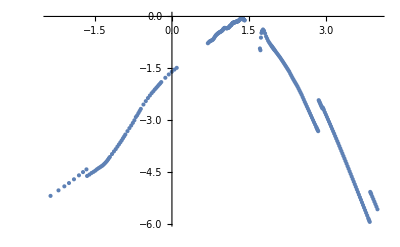

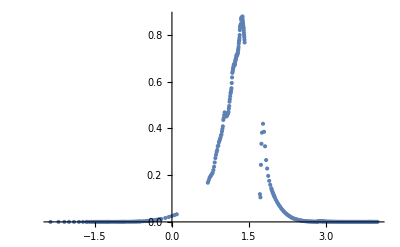

```mathematica
ELFFeData = Table[{ωFe[[i]],ELFFe[[i]]},{i,Length[ωFe]}];
logELFFeData =Table[{Log[10,ωFe[[i]]],ELFFe[[i]]},{i,Length[ωFe]}];
loglogELFFeData =Table[{Log[10,ωFe[[i]]],Log10[ELFFe[[i]]]},{i,Length[ωFe]}];
ListPlot[%,PlotRange->All]
ListPlot[%%%,PlotRange->All]
```

### Get Theory Prediction

#### Optical Mermin Function

We now consider the optical limit of the Mermin dielectric

```mathematica
(*ϵM[ω/(2 qF vF z),z,ν/(2 qF vF z)];
Limit[%,z->0]*)
```

The constants in the above can be written simply as the square of the Plasmon Frequency

```mathematica
4/3(qF vF χ)^2==4/3(ℏ/m(3 π^2 ne)^(2/3)√((m e^2)/(π ℏ^2(3 π^2 ne)^(1/3))1/(4 π ϵ0)))^2==ωp^2
```

4/3 qF^2 vF^2 χ^2==(e^2 ne)/(m ϵ0)==ωp^2

So our optical Mermin Dielectric is given by the simple expression below.

```mathematica
ϵMq0[ω,ν,ωp]
```

1-ωp^2/(ω (ⅈ ν+ω))

This is precisely the Drude Dielectric:

https://www.researchgate.net/publication/312007841_Dielectric_function_for_free_electron_gas_Comparison_between_Drude_and_Lindhard_models

#### Optical Loss Function

Using the Drude / Optical Mermin dielectric, we get the following loss function:

```mathematica
Information[ELFM0]
```

```mathematica
ELFM0[ω,ν,ωp]
```

(ν ω ωp^2)/(ν^2 ω^2+(ω^2-ωp^2)^2)

### Compare Data and Theory

#### Plot the two

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ"/.SIConstRepl) νZimanFaberLin[SIcrustparams],"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Orange,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"8 e^-"],ListPlot[loglogELFFeData,PlotRange->All]
}]
```

-Graphics-

#### Not so kosher adjustments to fit to the tail

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ"/.SIConstRepl) νZimanFaberLin[SIcrustparams],"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Orange,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"8 e^-"],Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ"/.SIConstRepl) νZimanFaberLin[SIParams[273,neSIIron[7800,0.5],0.5]],"ℏ" "ωp"/.SIParams[273,neSIIron[7800,0.5],0.5]]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Green,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"0.5 e^-"],Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ"/.SIConstRepl) νZimanFaberLin[SIParams[273,neSIIron[7800,0.5],0.5]],"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],Log10[Max[ωFe]]},PlotStyle->Red,PlotRange->All,AxesLabel->{"Log_10[ω] [eV]"},PlotLabel->"Log_10[Im[-1/ϵ_Fe]](ω)",PlotLabels->"0.5 e^- (fixed ω_p)"],ListPlot[loglogELFFeData,PlotRange->All]
}]
```

-Graphics-

this is not totally kosher, for the red curve,  which matches onto the tail, we are keeping the plasmon frequency fixed (so number of conduction electrons is fixed), but assuming the collision rate is one for an effective 0.5 electrons colliding.

#### Fit Drude Dielectric to the Tail

Here, we assume that we have correctly characterized the conduction electron number density (and hence the Plasmon Frequency).  As such we look to find the value of the collision frequency such that the theory prediction matches the low energy tail of the data (where we expect our model to be valid)

Isolate the low energy tail of the Loss Function Data

```mathematica
DataTail = SortBy[loglogELFFeData,First][[;;8]];
```

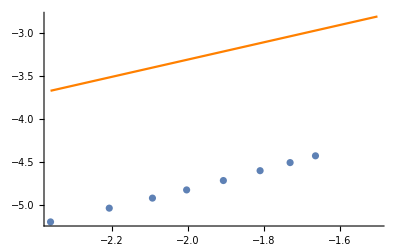

```mathematica
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,("ℏ" νZimanFaberLin[SIcrustparams]/.SIcrustparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],-1.5},PlotStyle->Orange,PlotRange->All],ListPlot[DataTail,PlotRange->All,AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_Fe](ω)"]
}]
```

Now we fit - Assuming the conduction electron number density is correct.

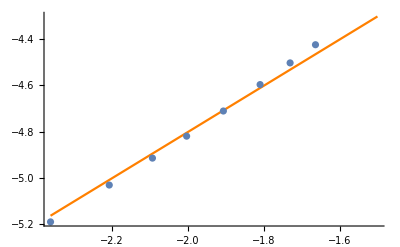

{νrescale→0.0319887}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
νrescale | 0.0319887 | 0.000666036 | 48.0286 | 4.43796×10^-10

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| DF | SS | MS
Model | 1 | 182.775 | 182.775
Error | 7 | 0.00457886 | 0.000654123
Uncorrected Total | 8 | 182.779 | 
Corrected Total | 7 | 0.493581 |

χ^2 / ndof is given by: error / MS

```mathematica
FeFit=NonlinearModelFit[DataTail,{Log10[ELFM0[10^ω "JpereV" /.SIConstRepl,νrescale ("ℏ" /.SIcrustparams) νZimanFaberLin[SIcrustparams] ,"ℏ""ωp"/.SIcrustparams]],νrescale>0},{νrescale},ω];
Show[{Plot[Log[10,ELFM0[10^ω "JpereV" /.SIConstRepl,(νrescale /.FeFit["BestFitParameters"])("ℏ" νZimanFaberLin[SIcrustparams]/.SIcrustparams),"ℏ" "ωp"/.SIcrustparams]],{ω,Log10[Min[ωFe]],-1.5},PlotStyle->Orange,PlotRange->All],ListPlot[DataTail,PlotRange->All,AxesLabel->{"ω [eV]"},PlotLabel->"Im[-1/ϵ_Fe](ω)"]
}]
FeFit["BestFitParameters"]
FeFit["ParameterTable"]
FeFit["ANOVATable"]
Print["χ^2 / ndof is given by: error / MS"]
```

Even with the 8 conduction electrons at the core, we match onto the tail to within a factor of 2

#### Expansion at the tail

It is also worth noting, that at the low energy tail:

```mathematica
{"ℏ""ωp","ℏ"νZimanFaberLin[SIcrustparams]}/.SIcrustparams
"JpereV" /.SIConstRepl (*>~ω at the tail*)
```

{4.8854×10^-18,7.36091×10^-18}

1.602×10^-19

So we can expand in small ω

```mathematica
Series[ELFM0[ω,ν, ωp],{ω,0,2}]
```

(ν ω)/ωp^2+O[ω]^3

#### n_eff Conclusion

As we showed above, the small discrepancy at the tail is alleviated when we take the number of conduction electrons in Iron to be smaller than those in the conduction band (8). However, 8 gives a slightly better fit to the position of the plasmon resonance, and is the number assumed given our conduction electron plasma model.

So we have good agreement with the data so long as we can have an ω dependent number of effective electrons. 

From the plot below found in Pines, it seems that there is precedent for this. Copper is also a transition metal like Iron and has almost exactly this behaviour. In fact, copper has 1 conduction / valence electron and has 0.5 effective electrons at low energies, precisely the rescaling we need to have Iron match the data. 
-Graphics-

#### 8 conduction electron fit Conclusions

We see from the above that we have almost perfectly matched the plasmon peak using 8 conduction electrons.

However, we miss the tail of the distribution, from above we’re off by a factor of 30. This can maybe be understood as either:
1) something to do with effective number of electrons, and a subtelty related to the fact that the valence second outermost electron shell in iron overlap (hence 8 instead of 2 conduction electrons)
	- see the not so kosher tab above
2) the neglect of ionic coherence / correlations from the structure / interference function as well as the psuedo potential above. 
	- either or both of which might significantly reduce the collision rate, or perhaps make it more sensitive to changes in effective number of electrons